```mathematica
Directory[]
```

/home/cmaier/Hackerspaces/FabLabNeckarAlb/Maerklin/MaerklinAnalysis/analysis

```mathematica
raw=Import["track.200us.10V.csv"];
```

```mathematica
Dimensions[raw]
```

{1048578,3}

```mathematica
Take[raw,5]
```

{{X,CH1,},{Second,Volt,},{-0.0179944,18.8,},{-0.0179943,18.8,},{-0.0179943,18.8,}}

```mathematica
Dimensions[timeseries=Most/@Drop[raw,2]]
```

{1048576,2}

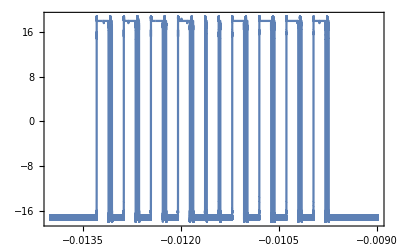

```mathematica
ListPlot[Take[timeseries,{80000,180000}],Frame->True,Joined->True]
```